# Lattice Cellular Automata.

## Luis Enrique Mateos Ruiz.

Cosas para que funcione.

```mathematica
n=20;(*Tamaño de la simulación*)
F[pos_,ar_]:=Table[{pos,ar[[i]]},{i,1,Length[ar[[2]]]}];(*Asigna a los vectores donde hay choques su nueva velocidad*)
g[x_]:=If[Sort[x]=={{-1,0},{1,0}}||Sort[x]=={{0,-1},{0,1}},RandomChoice[{{{0,1},{0,-1}},{{1,0},{-1,0}}}],If[Sort[x]=={{-1,0},{0,0},{1,0}}||Sort[x]=={{0,-1},{0,0},{0,1}},RandomChoice[{{{0,1},{0,0},{0,-1}},{{1,0},{0,0},{-1,0}}}],x]];
FF[r0_]:=-n Floor[(r0-{1,1})/n]+r0; (*Función de condiciones a la frontera*) 
F[pos_,ar_]:=Table[{pos,ar[[i]]},{i,1,Length[ar[[2]]]}];(*Función de nuevas velocidades en los puntos de colisión fuera del obstáculo*)
```

## Vectores del ciclo Do.

Vector R.

```mathematica
Vect={{0,0},{1,0},{0,1},{0,-1},{-1,0}};(*Vector de posibles posiciones*)
R=Flatten[Table[If[MemberQ[Flatten[Table[{i,j},{i,8,12},{j,8,12}],1],{i,j}],Nothing,{{i,j},RandomChoice[Vect]}],{i,1,n},{j,1,n}],1](*Vector de posiciones y paso posterior*)
```

{{{1,1},{0,-1}},{{1,2},{0,1}},{{1,3},{0,0}},{{1,4},{-1,0}},{{1,5},{0,0}},{{1,6},{-1,0}},{{1,7},{1,0}},{{1,8},{-1,0}},{{1,9},{0,-1}},{{1,10},{0,0}},{{1,11},{0,1}},{{1,12},{1,0}},{{1,13},{-1,0}},{{1,14},{0,0}},{{1,15},{0,-1}},{{1,16},{0,1}},{{1,17},{0,0}},{{1,18},{0,-1}},{{1,19},{-1,0}},{{1,20},{-1,0}},{{2,1},{0,1}},{{2,2},{-1,0}},{{2,3},{0,-1}},{{2,4},{0,-1}},{{2,5},{0,-1}},{{2,6},{1,0}},{{2,7},{0,0}},{{2,8},{0,-1}},{{2,9},{1,0}},{{2,10},{0,-1}},{{2,11},{0,0}},{{2,12},{1,0}},{{2,13},{0,1}},{{2,14},{0,0}},{{2,15},{0,1}},{{2,16},{0,-1}},{{2,17},{0,0}},{{2,18},{0,0}},{{2,19},{0,0}},{{2,20},{-1,0}},{{3,1},{0,-1}},{{3,2},{1,0}},{{3,3},{0,1}},{{3,4},{0,0}},{{3,5},{0,0}},{{3,6},{0,-1}},{{3,7},{0,-1}},{{3,8},{1,0}},{{3,9},{0,0}},{{3,10},{1,0}},{{3,11},{1,0}},{{3,12},{0,0}},{{3,13},{-1,0}},{{3,14},{-1,0}},{{3,15},{0,-1}},{{3,16},{0,0}},{{3,17},{1,0}},{{3,18},{0,0}},{{3,19},{0,0}},{{3,20},{1,0}},{{4,1},{0,0}},{{4,2},{0,1}},{{4,3},{0,-1}},{{4,4},{0,-1}},{{4,5},{0,-1}},{{4,6},{0,0}},{{4,7},{0,0}},{{4,8},{0,-1}},{{4,9},{0,1}},{{4,10},{0,-1}},{{4,11},{0,1}},{{4,12},{1,0}},{{4,13},{-1,0}},{{4,14},{0,1}},{{4,15},{-1,0}},{{4,16},{-1,0}},{{4,17},{0,-1}},{{4,18},{1,0}},{{4,19},{0,1}},{{4,20},{1,0}},{{5,1},{0,0}},{{5,2},{1,0}},{{5,3},{0,0}},{{5,4},{0,1}},{{5,5},{-1,0}},{{5,6},{0,0}},{{5,7},{0,-1}},{{5,8},{0,1}},{{5,9},{0,0}},{{5,10},{1,0}},{{5,11},{0,1}},{{5,12},{0,0}},{{5,13},{0,0}},{{5,14},{1,0}},{{5,15},{0,-1}},{{5,16},{0,-1}},{{5,17},{-1,0}},{{5,18},{0,1}},{{5,19},{-1,0}},{{5,20},{0,0}},{{6,1},{-1,0}},{{6,2},{0,0}},{{6,3},{-1,0}},{{6,4},{-1,0}},{{6,5},{0,1}},{{6,6},{0,1}},{{6,7},{0,-1}},{{6,8},{-1,0}},{{6,9},{0,0}},{{6,10},{-1,0}},{{6,11},{0,-1}},{{6,12},{0,1}},{{6,13},{1,0}},{{6,14},{0,0}},{{6,15},{1,0}},{{6,16},{0,-1}},{{6,17},{1,0}},{{6,18},{0,0}},{{6,19},{0,0}},{{6,20},{0,-1}},{{7,1},{0,-1}},{{7,2},{0,0}},{{7,3},{0,1}},{{7,4},{1,0}},{{7,5},{0,1}},{{7,6},{0,0}},{{7,7},{1,0}},{{7,8},{0,-1}},{{7,9},{0,0}},{{7,10},{0,1}},{{7,11},{-1,0}},{{7,12},{-1,0}},{{7,13},{0,1}},{{7,14},{0,0}},{{7,15},{1,0}},{{7,16},{1,0}},{{7,17},{1,0}},{{7,18},{-1,0}},{{7,19},{1,0}},{{7,20},{1,0}},{{8,1},{0,1}},{{8,2},{1,0}},{{8,3},{1,0}},{{8,4},{0,1}},{{8,5},{1,0}},{{8,6},{0,0}},{{8,7},{1,0}},{{8,13},{0,1}},{{8,14},{-1,0}},{{8,15},{1,0}},{{8,16},{1,0}},{{8,17},{-1,0}},{{8,18},{-1,0}},{{8,19},{-1,0}},{{8,20},{1,0}},{{9,1},{1,0}},{{9,2},{0,1}},{{9,3},{-1,0}},{{9,4},{1,0}},{{9,5},{1,0}},{{9,6},{0,0}},{{9,7},{0,0}},{{9,13},{0,0}},{{9,14},{0,1}},{{9,15},{0,-1}},{{9,16},{-1,0}},{{9,17},{0,0}},{{9,18},{-1,0}},{{9,19},{0,-1}},{{9,20},{0,0}},{{10,1},{0,0}},{{10,2},{1,0}},{{10,3},{0,1}},{{10,4},{0,0}},{{10,5},{0,0}},{{10,6},{0,1}},{{10,7},{0,-1}},{{10,13},{0,0}},{{10,14},{0,-1}},{{10,15},{0,0}},{{10,16},{0,-1}},{{10,17},{0,1}},{{10,18},{0,0}},{{10,19},{1,0}},{{10,20},{-1,0}},{{11,1},{0,1}},{{11,2},{-1,0}},{{11,3},{-1,0}},{{11,4},{-1,0}},{{11,5},{0,0}},{{11,6},{1,0}},{{11,7},{0,1}},{{11,13},{1,0}},{{11,14},{-1,0}},{{11,15},{-1,0}},{{11,16},{0,-1}},{{11,17},{1,0}},{{11,18},{0,1}},{{11,19},{0,0}},{{11,20},{0,0}},{{12,1},{-1,0}},{{12,2},{0,0}},{{12,3},{1,0}},{{12,4},{1,0}},{{12,5},{1,0}},{{12,6},{0,1}},{{12,7},{1,0}},{{12,13},{-1,0}},{{12,14},{0,1}},{{12,15},{0,-1}},{{12,16},{0,1}},{{12,17},{0,0}},{{12,18},{0,1}},{{12,19},{-1,0}},{{12,20},{1,0}},{{13,1},{0,0}},{{13,2},{0,0}},{{13,3},{-1,0}},{{13,4},{1,0}},{{13,5},{0,-1}},{{13,6},{0,0}},{{13,7},{1,0}},{{13,8},{0,-1}},{{13,9},{-1,0}},{{13,10},{0,1}},{{13,11},{0,0}},{{13,12},{-1,0}},{{13,13},{0,-1}},{{13,14},{1,0}},{{13,15},{0,1}},{{13,16},{-1,0}},{{13,17},{-1,0}},{{13,18},{-1,0}},{{13,19},{-1,0}},{{13,20},{0,-1}},{{14,1},{0,-1}},{{14,2},{0,-1}},{{14,3},{-1,0}},{{14,4},{0,1}},{{14,5},{1,0}},{{14,6},{0,-1}},{{14,7},{1,0}},{{14,8},{0,1}},{{14,9},{0,1}},{{14,10},{0,0}},{{14,11},{0,-1}},{{14,12},{0,-1}},{{14,13},{0,1}},{{14,14},{1,0}},{{14,15},{0,0}},{{14,16},{0,-1}},{{14,17},{1,0}},{{14,18},{0,0}},{{14,19},{-1,0}},{{14,20},{1,0}},{{15,1},{1,0}},{{15,2},{0,1}},{{15,3},{0,1}},{{15,4},{0,-1}},{{15,5},{0,-1}},{{15,6},{1,0}},{{15,7},{0,-1}},{{15,8},{0,1}},{{15,9},{0,1}},{{15,10},{1,0}},{{15,11},{-1,0}},{{15,12},{0,-1}},{{15,13},{-1,0}},{{15,14},{1,0}},{{15,15},{0,1}},{{15,16},{0,1}},{{15,17},{0,-1}},{{15,18},{0,0}},{{15,19},{-1,0}},{{15,20},{-1,0}},{{16,1},{0,-1}},{{16,2},{-1,0}},{{16,3},{0,-1}},{{16,4},{0,-1}},{{16,5},{1,0}},{{16,6},{0,-1}},{{16,7},{0,-1}},{{16,8},{1,0}},{{16,9},{0,0}},{{16,10},{0,-1}},{{16,11},{0,1}},{{16,12},{1,0}},{{16,13},{0,1}},{{16,14},{0,0}},{{16,15},{0,1}},{{16,16},{1,0}},{{16,17},{1,0}},{{16,18},{0,-1}},{{16,19},{-1,0}},{{16,20},{1,0}},{{17,1},{0,0}},{{17,2},{0,0}},{{17,3},{0,0}},{{17,4},{0,-1}},{{17,5},{0,0}},{{17,6},{-1,0}},{{17,7},{0,0}},{{17,8},{1,0}},{{17,9},{0,1}},{{17,10},{1,0}},{{17,11},{-1,0}},{{17,12},{0,1}},{{17,13},{0,-1}},{{17,14},{1,0}},{{17,15},{-1,0}},{{17,16},{0,1}},{{17,17},{1,0}},{{17,18},{1,0}},{{17,19},{-1,0}},{{17,20},{0,0}},{{18,1},{1,0}},{{18,2},{0,1}},{{18,3},{0,0}},{{18,4},{0,1}},{{18,5},{0,-1}},{{18,6},{1,0}},{{18,7},{0,0}},{{18,8},{0,-1}},{{18,9},{-1,0}},{{18,10},{1,0}},{{18,11},{-1,0}},{{18,12},{-1,0}},{{18,13},{1,0}},{{18,14},{1,0}},{{18,15},{-1,0}},{{18,16},{1,0}},{{18,17},{1,0}},{{18,18},{0,-1}},{{18,19},{0,1}},{{18,20},{0,-1}},{{19,1},{1,0}},{{19,2},{0,-1}},{{19,3},{0,0}},{{19,4},{0,-1}},{{19,5},{1,0}},{{19,6},{1,0}},{{19,7},{-1,0}},{{19,8},{0,1}},{{19,9},{0,-1}},{{19,10},{-1,0}},{{19,11},{0,1}},{{19,12},{0,0}},{{19,13},{-1,0}},{{19,14},{1,0}},{{19,15},{0,1}},{{19,16},{0,-1}},{{19,17},{1,0}},{{19,18},{0,1}},{{19,19},{0,-1}},{{19,20},{0,-1}},{{20,1},{0,-1}},{{20,2},{0,1}},{{20,3},{0,-1}},{{20,4},{-1,0}},{{20,5},{1,0}},{{20,6},{0,0}},{{20,7},{-1,0}},{{20,8},{0,0}},{{20,9},{0,0}},{{20,10},{0,1}},{{20,11},{-1,0}},{{20,12},{-1,0}},{{20,13},{0,-1}},{{20,14},{1,0}},{{20,15},{1,0}},{{20,16},{-1,0}},{{20,17},{-1,0}},{{20,18},{0,0}},{{20,19},{-1,0}},{{20,20},{0,-1}}}

El vector R  asignara velocidades aleatorias fuera de un cuadro(obstáculo), notemos que el vector R funciona con un ciclo If, este bucle unicamente asocia velocidades aleatorias a  los nodos que se encuentran fuera del cuadro.

### Posiciones en R.

Aquí se muestran las posiciones del vector R.

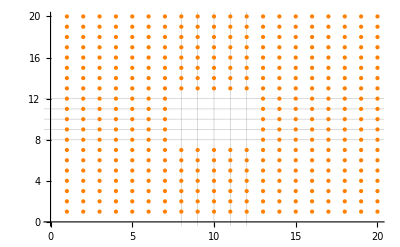

```mathematica
ListPlot[R[[All,1]],PlotStyle->Directive[PointSize[Medium],Orange],GridLines->{{8,9,10,11,12},{8,9,10,11,12}}]
```

Vector R2.

El vector R2 contiene las posición en el paso de tiempo siguiente, sin aplicarle la función de condiciones a la frontera.

```mathematica
R2=Table[R[[i,1]]+R[[i,2]],{i,1,Length[R]}]
```

{{1,0},{1,3},{1,3},{0,4},{1,5},{0,6},{2,7},{0,8},{1,8},{1,10},{1,12},{2,12},{0,13},{1,14},{1,14},{1,17},{1,17},{1,17},{0,19},{0,20},{2,2},{1,2},{2,2},{2,3},{2,4},{3,6},{2,7},{2,7},{3,9},{2,9},{2,11},{3,12},{2,14},{2,14},{2,16},{2,15},{2,17},{2,18},{2,19},{1,20},{3,0},{4,2},{3,4},{3,4},{3,5},{3,5},{3,6},{4,8},{3,9},{4,10},{4,11},{3,12},{2,13},{2,14},{3,14},{3,16},{4,17},{3,18},{3,19},{4,20},{4,1},{4,3},{4,2},{4,3},{4,4},{4,6},{4,7},{4,7},{4,10},{4,9},{4,12},{5,12},{3,13},{4,15},{3,15},{3,16},{4,16},{5,18},{4,20},{5,20},{5,1},{6,2},{5,3},{5,5},{4,5},{5,6},{5,6},{5,9},{5,9},{6,10},{5,12},{5,12},{5,13},{6,14},{5,14},{5,15},{4,17},{5,19},{4,19},{5,20},{5,1},{6,2},{5,3},{5,4},{6,6},{6,7},{6,6},{5,8},{6,9},{5,10},{6,10},{6,13},{7,13},{6,14},{7,15},{6,15},{7,17},{6,18},{6,19},{6,19},{7,0},{7,2},{7,4},{8,4},{7,6},{7,6},{8,7},{7,7},{7,9},{7,11},{6,11},{6,12},{7,14},{7,14},{8,15},{8,16},{8,17},{6,18},{8,19},{8,20},{8,2},{9,2},{9,3},{8,5},{9,5},{8,6},{9,7},{8,14},{7,14},{9,15},{9,16},{7,17},{7,18},{7,19},{9,20},{10,1},{9,3},{8,3},{10,4},{10,5},{9,6},{9,7},{9,13},{9,15},{9,14},{8,16},{9,17},{8,18},{9,18},{9,20},{10,1},{11,2},{10,4},{10,4},{10,5},{10,7},{10,6},{10,13},{10,13},{10,15},{10,15},{10,18},{10,18},{11,19},{9,20},{11,2},{10,2},{10,3},{10,4},{11,5},{12,6},{11,8},{12,13},{10,14},{10,15},{11,15},{12,17},{11,19},{11,19},{11,20},{11,1},{12,2},{13,3},{13,4},{13,5},{12,7},{13,7},{11,13},{12,15},{12,14},{12,17},{12,17},{12,19},{11,19},{13,20},{13,1},{13,2},{12,3},{14,4},{13,4},{13,6},{14,7},{13,7},{12,9},{13,11},{13,11},{12,12},{13,12},{14,14},{13,16},{12,16},{12,17},{12,18},{12,19},{13,19},{14,0},{14,1},{13,3},{14,5},{15,5},{14,5},{15,7},{14,9},{14,10},{14,10},{14,10},{14,11},{14,14},{15,14},{14,15},{14,15},{15,17},{14,18},{13,19},{15,20},{16,1},{15,3},{15,4},{15,3},{15,4},{16,6},{15,6},{15,9},{15,10},{16,10},{14,11},{15,11},{14,13},{16,14},{15,16},{15,17},{15,16},{15,18},{14,19},{14,20},{16,0},{15,2},{16,2},{16,3},{17,5},{16,5},{16,6},{17,8},{16,9},{16,9},{16,12},{17,12},{16,14},{16,14},{16,16},{17,16},{17,17},{16,17},{15,19},{17,20},{17,1},{17,2},{17,3},{17,3},{17,5},{16,6},{17,7},{18,8},{17,10},{18,10},{16,11},{17,13},{17,12},{18,14},{16,15},{17,17},{18,17},{18,18},{16,19},{17,20},{19,1},{18,3},{18,3},{18,5},{18,4},{19,6},{18,7},{18,7},{17,9},{19,10},{17,11},{17,12},{19,13},{19,14},{17,15},{19,16},{19,17},{18,17},{18,20},{18,19},{20,1},{19,1},{19,3},{19,3},{20,5},{20,6},{18,7},{19,9},{19,8},{18,10},{19,12},{19,12},{18,13},{20,14},{19,16},{19,15},{20,17},{19,19},{19,18},{19,19},{20,0},{20,3},{20,2},{19,4},{21,5},{20,6},{19,7},{20,8},{20,9},{20,11},{19,11},{19,12},{20,12},{21,14},{21,15},{19,16},{19,17},{20,18},{19,19},{20,19}}

### Posiciones en R2.

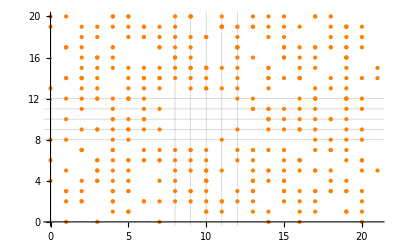

```mathematica
ListPlot[R2,PlotStyle->Directive[PointSize[Medium],Orange],GridLines->{{8,9,10,11,12},{8,9,10,11,12}}]
```

Vector R3.

R3 contiene las posiciones del paso de tiempo siguiente con la función de condiciones a la frontera, también  contiene la velocidad del vector que tomó la nueva posición.

### Posiciones de R3.

Notemos que todas las posiciones se encuentran dentro del cuadro, y que las posiciones que caen en la frontera del obstáculo no han cambiado aún.

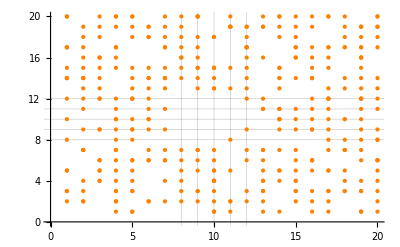

```mathematica
R3=Table[{FF[R[[i,1]]+R[[i,2]]],R[[i,2]]},{i,1,Length[R]}];
ListPlot[R3[[All,1]],PlotStyle->Directive[PointSize[Medium],Orange],GridLines->{{8,9,10,11,12},{8,9,10,11,12}}]
```

Vector c1.

El vector c1 cuenta cuantas colisiones hay en cada nodo.

```mathematica
c1=Flatten[Table[{{i,j},Count[R2,{i,j}]},{i,1,n},{j,1,n}],1];
```

Vector pos.

### pos: este vector guarda los vectores donde hay dos o tres colisiones(aunque sean parte de la frontera; una esquina).

{{1,3},{1,14},{2,2},{3,4},{3,5},{3,6},{3,9},{3,12},{3,16},{4,2},{4,3},{4,7},{4,10},{4,17},{4,20},{5,1},{5,3},{5,6},{5,9},{5,20},{6,2},{6,6},{6,10},{6,14},{6,18},{6,19},{7,6},{7,17},{8,16},{9,3},{9,7},{9,15},{10,1},{10,5},{10,13},{10,18},{11,2},{12,19},{13,3},{13,4},{13,7},{13,11},{13,19},{14,5},{14,11},{14,14},{14,15},{15,3},{15,4},{15,16},{15,17},{16,9},{17,3},{17,5},{17,17},{17,20},{18,3},{18,10},{18,17},{19,1},{19,3},{19,17},{20,6},{1,17},{2,7},{2,14},{5,12},{7,14},{9,20},{10,15},{14,10},{16,6},{16,14},{17,12},{18,7},{19,12},{19,16},{19,19}}

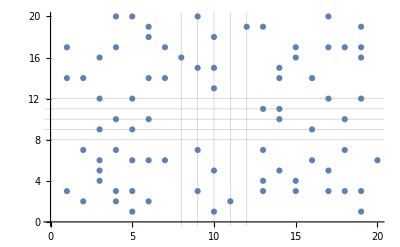

```mathematica
pos=Flatten[Table[Select[c1,#[[2]]==j&][[All,1]],{j,2,3}],1]
ListPlot[pos,GridLines->{{8,9,10,11,12},{8,9,10,11,12}}]
```

### pos: guarda los vectores donde hay una o dos colisiones(de esta lista se extraerán los vectores de la frontera del obstáculo donde hay colisiones ya sea una o dos en el caso de las esquinas).

{{1,2},{1,5},{1,8},{1,10},{1,12},{1,20},{2,3},{2,4},{2,9},{2,11},{2,12},{2,13},{2,15},{2,16},{2,17},{2,18},{2,19},{3,13},{3,14},{3,15},{3,18},{3,19},{4,1},{4,4},{4,5},{4,6},{4,8},{4,9},{4,11},{4,12},{4,15},{4,16},{4,19},{5,4},{5,5},{5,8},{5,10},{5,13},{5,14},{5,15},{5,18},{5,19},{6,7},{6,9},{6,11},{6,12},{6,13},{6,15},{7,2},{7,4},{7,7},{7,9},{7,11},{7,13},{7,15},{7,18},{7,19},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,14},{8,15},{8,17},{8,18},{8,19},{8,20},{9,2},{9,5},{9,6},{9,13},{9,14},{9,16},{9,17},{9,18},{10,2},{10,3},{10,6},{10,7},{10,14},{11,1},{11,5},{11,8},{11,13},{11,15},{11,20},{12,2},{12,3},{12,6},{12,7},{12,9},{12,12},{12,13},{12,14},{12,15},{12,16},{12,18},{13,1},{13,2},{13,5},{13,6},{13,12},{13,16},{13,20},{14,1},{14,4},{14,7},{14,9},{14,13},{14,18},{14,19},{14,20},{15,2},{15,5},{15,6},{15,7},{15,9},{15,10},{15,11},{15,14},{15,18},{15,19},{15,20},{16,1},{16,2},{16,3},{16,5},{16,10},{16,11},{16,12},{16,15},{16,16},{16,17},{16,19},{17,1},{17,2},{17,7},{17,8},{17,9},{17,10},{17,11},{17,13},{17,15},{17,16},{18,4},{18,5},{18,8},{18,13},{18,14},{18,18},{18,19},{18,20},{19,4},{19,6},{19,7},{19,8},{19,9},{19,10},{19,11},{19,13},{19,14},{19,15},{19,18},{20,1},{20,2},{20,3},{20,5},{20,8},{20,9},{20,11},{20,12},{20,14},{20,17},{20,18},{20,19},{1,3},{1,14},{2,2},{3,4},{3,5},{3,6},{3,9},{3,12},{3,16},{4,2},{4,3},{4,7},{4,10},{4,17},{4,20},{5,1},{5,3},{5,6},{5,9},{5,20},{6,2},{6,6},{6,10},{6,14},{6,18},{6,19},{7,6},{7,17},{8,16},{9,3},{9,7},{9,15},{10,1},{10,5},{10,13},{10,18},{11,2},{12,19},{13,3},{13,4},{13,7},{13,11},{13,19},{14,5},{14,11},{14,14},{14,15},{15,3},{15,4},{15,16},{15,17},{16,9},{17,3},{17,5},{17,17},{17,20},{18,3},{18,10},{18,17},{19,1},{19,3},{19,17},{20,6}}

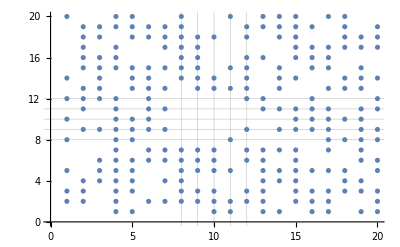

```mathematica
pos1=Flatten[Table[Select[c1,#[[2]]==j&][[All,1]],{j,1,2}],1]
ListPlot[pos1,GridLines->{{8,9,10,11,12},{8,9,10,11,12}}]
```

### Pos: guarda los vectores de dos o tres colisiones pero quitándole los de la frontera; el caso de una esquina donde hay dos colisiones.

```mathematica
Pos=Flatten[Table[Select[pos,#==R[[i,1]]&],{i,1,Length[R]}],1];
```

```mathematica
ListPlot[Pos,GridLines->{{8,9,10,11,12},{8,9,10,11,12}}]
```

-Graphics-

### Pos1: ya es el vector que selecciona cuales vectores de la frontera tuvieron colisiones.

```mathematica
Pos1=Flatten[Table[Select[pos1,#==Fr[[i]]&],{i,1,Length[Fr]}],1]
```

{{11,8},{12,9},{12,12}}

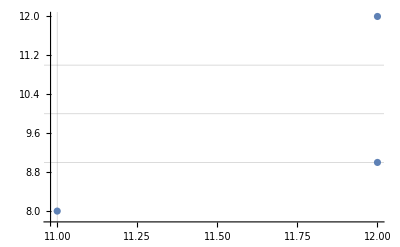

```mathematica
ListPlot[Pos1,GridLines->{{9,10,11},{9,10,11}}]
```

### Pos2: este vector asigna a cada vector donde hubo una colisión su nueva velocidad de acuerdo con la función de colisiones, en este caso Pos2 tiene las colisiones fuera del obstáculo con sus nuevas velocidades.

```mathematica
Pos2=Flatten[Table[F[Pos[[i]],g[Select[R3,#[[1]]==Pos[[i]]&][[All,2]]]],{i,1,Length[Pos]}],0];
```

```mathematica
Table[Select[R3,#[[1]]==Pos[[i]]&][[All,2]],{i,1,Length[Pos]}];
```

```mathematica
Pos
```

{{1,3},{1,14},{1,17},{2,2},{2,7},{2,14},{3,4},{3,5},{3,6},{3,9},{3,12},{3,16},{4,2},{4,3},{4,7},{4,10},{4,17},{4,20},{5,1},{5,3},{5,6},{5,9},{5,12},{5,20},{6,2},{6,6},{6,10},{6,14},{6,18},{6,19},{7,6},{7,14},{7,17},{8,16},{9,3},{9,7},{9,15},{9,20},{10,1},{10,5},{10,13},{10,15},{10,18},{11,2},{12,19},{13,3},{13,4},{13,7},{13,11},{13,19},{14,5},{14,10},{14,11},{14,14},{14,15},{15,3},{15,4},{15,16},{15,17},{16,6},{16,9},{16,14},{17,3},{17,5},{17,12},{17,17},{17,20},{18,3},{18,7},{18,10},{18,17},{19,1},{19,3},{19,12},{19,16},{19,17},{19,19},{20,6}}

### Pos12:Vector que da a los nodos de la frontera la nueva velocidad, a este vector se le aplica la nueva función g1 de colisiones para los punto del obstáculo

```mathematica
Pos12=Flatten[Table[F1[Pos1[[i]],g1[Select[R3,#[[1]]==Pos1[[i]]&][[All,2]]]],{i,1,Length[Pos1]}],0]
```

{{{{11,8},{0,-1}}},{{{12,9},{0,0}}},{{{12,12},{0,0}}}}

```mathematica
Table[Select[R3,#[[1]]==Pos1[[i]]&][[All,2]],{i,1,Length[Pos1]}]
```

{{{0,1}},{{-1,0}},{{-1,0}}}

```mathematica
Pos1
```

{{11,8},{12,9},{12,12}}

### Tot: Junta las dos listas de colisiones con la nueva velocidad.

```mathematica
Tot=Sort[Join[Pos2,Pos12]]
```

{{{{11,8},{0,-1}}},{{{12,9},{0,0}}},{{{12,12},{0,0}}},{{{1,3},{0,1}},{{1,3},{0,0}}},{{{1,14},{0,0}},{{1,14},{0,-1}}},{{{1,17},{0,1}},{{1,17},{0,0}}},{{{2,2},{1,0}},{{2,2},{-1,0}}},{{{2,7},{1,0}},{{2,7},{0,0}}},{{{2,14},{0,1}},{{2,14},{0,0}}},{{{3,4},{0,1}},{{3,4},{0,0}}},{{{3,5},{0,0}},{{3,5},{0,-1}}},{{{3,6},{1,0}},{{3,6},{0,-1}}},{{{3,9},{1,0}},{{3,9},{0,0}}},{{{3,12},{1,0}},{{3,12},{0,0}}},{{{3,16},{0,0}},{{3,16},{-1,0}}},{{{4,2},{1,0}},{{4,2},{0,-1}}},{{{4,3},{1,0}},{{4,3},{-1,0}}},{{{4,7},{0,0}},{{4,7},{0,-1}}},{{{4,10},{1,0}},{{4,10},{0,1}}},{{{4,17},{1,0}},{{4,17},{-1,0}}},{{{4,20},{1,0}},{{4,20},{0,1}}},{{{5,1},{0,0}},{{5,1},{-1,0}}},{{{5,3},{0,0}},{{5,3},{-1,0}}},{{{5,6},{0,0}},{{5,6},{0,-1}}},{{{5,9},{0,1}},{{5,9},{0,0}}},{{{5,12},{1,0}},{{5,12},{0,1}}},{{{5,20},{1,0}},{{5,20},{0,0}}},{{{6,2},{1,0}},{{6,2},{0,0}}},{{{6,6},{1,0}},{{6,6},{-1,0}}},{{{6,10},{1,0}},{{6,10},{0,-1}}},{{{6,14},{1,0}},{{6,14},{0,0}}},{{{6,18},{0,0}},{{6,18},{-1,0}}},{{{6,19},{0,0}},{{6,19},{0,-1}}},{{{7,6},{0,1}},{{7,6},{0,0}}},{{{7,14},{0,1}},{{7,14},{0,0}}},{{{7,17},{0,1}},{{7,17},{0,-1}}},{{{8,16},{0,1}},{{8,16},{0,-1}}},{{{9,3},{1,0}},{{9,3},{0,1}}},{{{9,7},{1,0}},{{9,7},{0,0}}},{{{9,15},{1,0}},{{9,15},{0,1}}},{{{9,20},{0,1}},{{9,20},{0,0}}},{{{10,1},{1,0}},{{10,1},{0,0}}},{{{10,5},{1,0}},{{10,5},{0,0}}},{{{10,13},{0,0}},{{10,13},{0,-1}}},{{{10,15},{0,0}},{{10,15},{0,-1}}},{{{10,18},{0,1}},{{10,18},{0,0}}},{{{11,2},{1,0}},{{11,2},{0,1}}},{{{12,19},{0,1}},{{12,19},{-1,0}}},{{{13,3},{1,0}},{{13,3},{-1,0}}},{{{13,4},{1,0}},{{13,4},{0,-1}}},{{{13,7},{1,0}},{{13,7},{0,-1}}},{{{13,11},{0,1}},{{13,11},{0,0}}},{{{13,19},{0,-1}},{{13,19},{-1,0}}},{{{14,5},{1,0}},{{14,5},{-1,0}}},{{{14,10},{1,0}},{{14,10},{0,0}}},{{{14,11},{0,-1}},{{14,11},{-1,0}}},{{{14,14},{1,0}},{{14,14},{0,1}}},{{{14,15},{0,0}},{{14,15},{0,-1}}},{{{15,3},{1,0}},{{15,3},{-1,0}}},{{{15,4},{0,1}},{{15,4},{0,-1}}},{{{15,16},{0,1}},{{15,16},{0,-1}}},{{{15,17},{1,0}},{{15,17},{0,1}}},{{{16,6},{1,0}},{{16,6},{0,-1}}},{{{16,9},{0,0}},{{16,9},{0,-1}}},{{{16,14},{1,0}},{{16,14},{0,1}}},{{{17,3},{0,0}},{{17,3},{0,-1}}},{{{17,5},{1,0}},{{17,5},{0,0}}},{{{17,12},{1,0}},{{17,12},{0,-1}}},{{{17,17},{1,0}},{{17,17},{0,1}}},{{{17,20},{1,0}},{{17,20},{0,0}}},{{{18,3},{0,1}},{{18,3},{0,0}}},{{{18,7},{0,0}},{{18,7},{0,-1}}},{{{18,10},{1,0}},{{18,10},{-1,0}}},{{{18,17},{1,0}},{{18,17},{0,-1}}},{{{19,1},{1,0}},{{19,1},{0,-1}}},{{{19,3},{0,0}},{{19,3},{0,-1}}},{{{19,12},{0,1}},{{19,12},{0,0}}},{{{19,16},{1,0}},{{19,16},{0,1}}},{{{19,17},{0,1}},{{19,17},{0,-1}}},{{{19,19},{0,1}},{{19,19},{0,-1}}},{{{20,6},{1,0}},{{20,6},{0,0}}}}

```mathematica
Tot[[11,1,1]]
```

{3,5}

### Rt: ahora Rt en el ciclo se evalua en Tot pues ahí están las nuevas posiciones para la frontera y para los puntos fuera de ella donde hubo colisiones.

```mathematica
Rt=Sort[R3];
Do[R4=Join[Select[Rt,#[[1]]≠Tot[[j,1,1]]&],Tot[[j]]];
Rt=Sort[R4],{j,1,Length[Tot]}];
```

### Función de colisiones para los puntos de la frontera del obstáculo.

Funciona muy análoga a g, fue necesario hacerla puesto que aquí se pueden evaluar nodos con una sola partícula.

```mathematica
g1[x1_]:=If[x1=={{0,1}}||x1=={{0,-1}}||x1=={{1,0}}||x1=={{-1,0}},RandomChoice[{-x1,{{0,0}}}],
If[Sort[x1]=={{0,1},{1,0}}||Sort[x1]=={{-1,0},{0,1}}||Sort[x1]=={{-1,0},{0,-1}}||Sort[x1]=={{0,-1},{1,0}},RandomChoice[{-x1,{{0,0},{0,0}}}],x1]];
```

```mathematica
g1[{{0,1},{1,0}}]
```

{{0,0},{0,0}}

```mathematica
g1[{{1,0}}]
```

{{0,0}}

### Función F1.

De igual forma que para g1, se hizo una función F1 análoga a F para los puntos de la frontera.

```mathematica
F1[pos1_,ar1_]:=If[Length[ar1]==1,Table[{pos1,ar1[[k]]},{k,1}],Table[{pos1,ar1[[k]]},{k,1,2}]];
```

Otros.

### Función que da la caja con el hueco cuadrado.

```mathematica
H[v_]:=If[MemberQ[Flatten[Table[{i,j},{i,8,12},{j,8,12}],1],v],Nothing,v];
```

```mathematica
H[{8,8}]
```

Nothing

```mathematica
n=20;
```

### Vectores de la caja cuadrada.

```mathematica
Fr=Flatten[Table[{If[MemberQ[Flatten[Table[{i,j},{i,8,12},{j,8,12}],1],{i,j}],{i,j},Nothing]},{i,1,n},{j,1,n}],2]
```

{{8,8},{8,9},{8,10},{8,11},{8,12},{9,8},{9,9},{9,10},{9,11},{9,12},{10,8},{10,9},{10,10},{10,11},{10,12},{11,8},{11,9},{11,10},{11,11},{11,12},{12,8},{12,9},{12,10},{12,11},{12,12}}

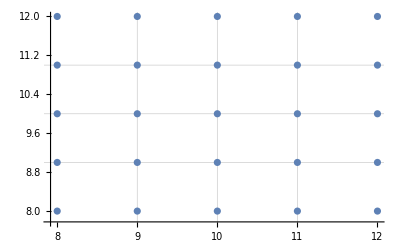

```mathematica
ListPlot[Fr,GridLines->{{9,10,11},{9,10,11}}]
```

Conclusiones.

Los autómatas celulares son funciones matemáticas dinámicas que ayudan a simular modelos de movimiento de fluidos. Esta técnica es una alternativa a los métodos en los que se resuelven las ecuaciones de Navier-Stokes. En este método se presenta la idea de la discretization de la materia, en lugar de tratarla como un continuo. Para interpretarse en el mundo macroscópico se recurre a la física estadista.